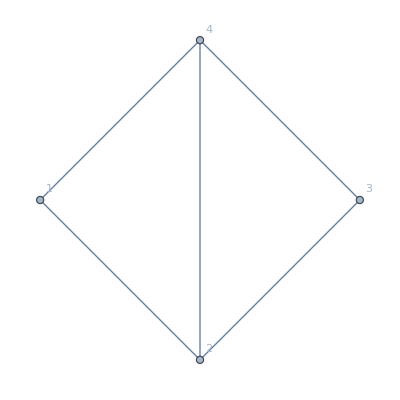

```mathematica
g=EdgeAdd[Graph[CycleGraph[4],VertexLabels->"Name"],{2<->4}]
```

```mathematica
ChromaticPolynomial[g,x]
```

-4 x+8 x^2-5 x^3+x^4

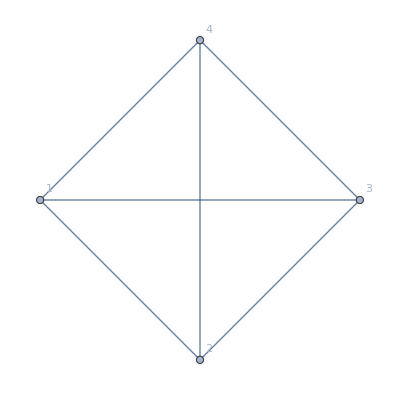

```mathematica
h=EdgeAdd[g,{1<->3}]
```

```mathematica
ChromaticPolynomial[h,x]/ChromaticPolynomial[g,x]/.x->4
```

1/2